```mathematica
Remove["Global`*"]
```

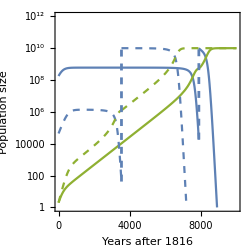

```mathematica
PlotTraj = Table[0,{2}];
KTable = {600*10^6,1.383*10^6};
DTable = {178*10^6,44000};
CompDynStart[rh_,rm_,ahm_,c_,k1_,InitialH_,T_] :=

NDSolve[{
H'[t] ==rh*H[t]*(1-(H[t]+ahm*M[t])/k1),
M'[t] ==rm*M[t]*(1-(M[t]+(ahm/c)*H[t])/k1),
H[0]==InitialH,M[0]==2,
WhenEvent[
M[t]==0.9*(k1),
end=t;
Hend = H[t];
Mend = M[t];
"StopIntegration"
]
},{H,M},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
CompDynEnd[rh_,rm_,ahm_,c_,k2_,T_,Mstart_,Tstart_] :=

NDSolve[{
H'[t] ==rh*H[t]*(1-(H[t]+ahm*M[t])/k2),
M'[t] ==rm*M[t]*(1-(M[t]+(ahm/c)*H[t])/k2),
H[Tstart]==10*10^9,M[Tstart]==Mstart
},{H,M},{t,Tstart,T},MaxSteps->Infinity,InterpolationOrder->All];


i=1;
With[{rh=0.0067,rm=0.0067*1.5,ahm=8,c=10,InitialH=DTable[[i]],k1=KTable[[i]],k2=10*10^9,T=10^4},
Quiet[Traj1=Evaluate[{H[t],M[t]}/.CompDynStart[rh,rm,ahm,c,k1,InitialH,T] ]];
Mstart = Mend;
Tstart = end;
Quiet[Traj2=Evaluate[{H[t],M[t]}/.CompDynEnd[rh,rm,ahm,c,k2,T,Mstart,Tstart] ]];
PlotTraj1=Show[{
LogPlot[Traj1,{t,0,end},PlotRange->{{0,T},{1,10^12}},AspectRatio->1,Frame->True,FrameLabel->{"Years after 1816","Population size"},PlotStyle->{ColorData[97,1],ColorData[97,3]}(*,PlotLegends->SwatchLegend[{"Humans","Creatures"}]*)],
LogPlot[Traj2,{t,end,T},PlotRange->{1,All},PlotStyle->{ColorData[97,1],ColorData[97,3]}],
Graphics[{ColorData[97,1],Dashed,Thickness[0.008],Line[{{end,Log@Hend},{end,Log@(10*10^9)}}]}]
}];
];
i=2;
With[{rh=0.0067,rm=0.0067*1.5,ahm=8,c=10,InitialH=DTable[[i]],k1=KTable[[i]],k2=10*10^9,T=10^4},
Quiet[Traj1=Evaluate[{H[t],M[t]}/.CompDynStart[rh,rm,ahm,c,k1,InitialH,T] ]];
Mstart = Mend;
Tstart = end;
Quiet[Traj2=Evaluate[{H[t],M[t]}/.CompDynEnd[rh,rm,ahm,c,k2,T,Mstart,Tstart] ]];
PlotTraj2=Show[{
LogPlot[Traj1,{t,0,end},PlotRange->{{0,T},{1,10^12}},AspectRatio->1,Frame->True,FrameLabel->{"Years after 1816","Population density"},PlotStyle->{Directive[Dashed,ColorData[97,1]],Directive[Dashed,ColorData[97,3]]}],
LogPlot[Traj2,{t,end,T},PlotRange->{1,All},PlotStyle->{Directive[Dashed,ColorData[97,1]],Directive[Dashed,ColorData[97,3]]}],
Graphics[{ColorData[97,1],Dashed,Thickness[0.008],Line[{{end,Log@Hend},{end,Log@(10*10^9)}}]}]
}];
];
CombinedPlot=Show[{PlotTraj1,PlotTraj2},ImageSize->250]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_traj.pdf",CombinedPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_traj.pdf

```mathematica
AMCurves = Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_textam2_lowdeath2k.csv","Table"];
EUCurves= Import["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/d_textEU_lowdeath2k.csv","Table"];
```

```mathematica
Compt = Table[i,{i,1,10,0.05}];
EUValues = Table[Transpose[{Table[i,{i,1,10,0.05}],EUCurves[[All,j]]}],{j,1,10,1}];
AMValues = Table[Transpose[{Table[i,{i,1,10,0.05}],AMCurves[[All,j]]}],{j,1,10,1}];
```

```mathematica
Dimensions[EUCurves]
```

{181,10}

```mathematica
Length[Compt]
```

181

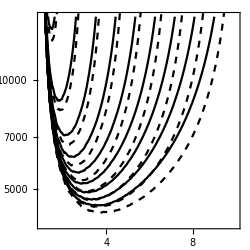

```mathematica
CompPlot=Show[{
ListLogPlot[EUValues,PlotStyle->Directive[Black],Joined->True,PlotRange->{{1,10},{4000,15000}},Frame->True],
ListLogPlot[AMValues,PlotStyle->Directive[Black,Dashed],Joined->True]
},AspectRatio->1,ImageSize->250]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_complot.pdf",CompPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2016_Frankenstein/fig_complot.pdf